# Inverted spherical pendulum

## Feedback linearization

Feedback linearization of the non linear system of the inverted spherical pendulum. 
The model was derived from an examination in the “Meccanica dei robot” course instructed by Professor Gabiccini.
The scheme of the model is shown in the image below.
-Graphics-

## Packages

```mathematica
Directory[];
SetDirectory["C:\\Users\\Giorgia\\Desktop\\TAVOLA2"];
Get["ScrewCalculusPro.m", Path->"C:\\Users\\Giorgia\\Desktop\\TAVOLA2"];
```

## Initialization

To model the inverted spherical pendulum only 4 variables are sufficient: 
- θr: the rotation angle of the right wheel
- θl: the rotation angle of the left wheel
- ψ: X rotation in the XYZ parametrization
- ϕ: Y rotation in the XYZ parametrization

```mathematica
q[t_]={θr[t],θl[t],ψ[t],ϕ[t]};
qd[t_]=D[q[t],t];
qdd[t_]=D[qd[t],t];

params = {G-> 9.81,mp->1.,ma->1 ,mr-> 0.5,lp-> 0.7,la-> 1,  r-> 0.3, Ia-> 0.8 };
```

## Rolling without slipping constraint

```mathematica
θ=r/la(q[t][[1]]-q[t][[2]]);
xd=r/2*Cos[θ]*(qd[t][[1]]+qd[t][[2]]);
yd=r/2*Sin[θ]*(qd[t][[1]]+qd[t][[2]]);
```

## Kinematics

To compute the model kinematics we derive the Lagrangian from the kinetics and potential energies.

```mathematica
va={xd,yd,0};
wrr={θr'[t],0,D[θ,t]};
wrl={θl'[t],0,D[θ,t]};
vrr=θr'[t]*r;
vrl=θl'[t]*r;
```

XYZ parameterization:  ψ along X, ϕ along Y e θ along Z

```mathematica
Rz[ϵ_]=RotationMatrix[ϵ,{0,0,1}];
Ry[ϵ_]=RotationMatrix[ϵ,{0,1,0}];
Rx[ϵ_]=RotationMatrix[ϵ,{1,0,0}];
Rp=Rx[ψ[t]].Ry[ϕ[t]].Rz[η[t]];

AP=Rp.{0,0,lp/2};
dAP=D[AP,t];

Subscript[wP, g]= ψ'[t]*{1,0,0}+ϕ'[t]*Rx[ψ[t]].{0,1,0}+η'[t]*Rx[ψ[t]].Ry[ϕ[t]].{0,0,1};
Subscript[wP, p]=η'[t]*{0,0,1}+ϕ'[t]*Transpose[Rz[η[t]]].{0,1,0}+ψ'[t]*Transpose[Ry[ϕ[t]].Rz[η[t]]].{1,0,0};

Subscript[wP, s]=Rp.Subscript[wP, p];
vP=va+Subscript[wP, s] × AP;

Jr={{1/2*mr*r^2,0,0},{0,1/4*mr*r^2,0},{0,0,1/4*mr*r^2}};
Jp={{1/12*mp*lp^2,0,0},{0,1/12*mp*lp^2,0},{0,0,0}};

Jpg=Simplify[Rp.Jp.Transpose[Rp]];
```

## Kinetics energy

### Pendulum

```mathematica
Ep1=Simplify[1/2*mp*vP.vP];
Ep2=Simplify[1/2*Subscript[wP, s].Jpg.Subscript[wP, s]];
```

### Axes

```mathematica
Ea1=1/2*mp*va.va;
Ea2=1/2*Ia*θ*θ;
```

### Wheels

```mathematica
Ewl1=1/2*mr*vrr^2;
Ewr1=1/2*mr*vrl^2;
Ewl2=1/2*wrr.Jr.wrr;
Ewr2=1/2*wrl.Jr.wrl;
```

Total kinetics energy:

```mathematica
Etot=Simplify[Ewl1+Ewl2+Ewr1+Ewr2+Ep1+Ep2];
```

## Potential energy

```mathematica
U=mp*G*AP[[3]];
```

## Lagrangian

```mathematica
L = Etot-U;
Emec=Etot+U;
```

## Equations of motion

```mathematica
DynLeftTerm = Simplify[D[D[L,{qd[t]}],t]-D[L,{q[t]}]]; (* Left term of the forward kinematics *)

Mq = Simplify[D[DynLeftTerm,{qdd[t]}]]; (* Mass matrix *)
Cq = Simplify[InertiaToCoriolis[Mq,q[t],qd[t]]]; (* Coriolis matrix *)
Gq = Simplify[DynLeftTerm-Mq.qdd[t]-Cq.qd[t]]; (* Gravity vector *)
```

## Feedback linearization tools

### Lie Brackets

```mathematica
LieBracketScalar[f_,λ_,x_]:=D[λ,{x}].f;
LieBracketVector[f_,g_,x_]:=D[g,{x}].f - D[f,{x}].g;
LieBracketCovector[f_,ω_,x_]:=f.Transpose[D[ω,{x}]]+ω.D[f,{x}];
```

### Lie brackets and filtration on distributions

```mathematica
LieBracketDist[Δa_,Δb_,x_]:= Block[{brackets},
(*!!!x va passato come vettore riga, come in LieBracketVector!!!*)
brackets=ArrayReshape[{Δa[[;;,1]]},{Length[x],1}];
Do[{
Do[
brackets=ArrayFlatten[{{brackets,ArrayReshape[LieBracketVector[Δa[[;;,i]],Δb[[;;,j]],x],{Length[x],1}]}}],
{j,Dimensions[Δb][[2]]}]
},
{i,Dimensions[Δa][[2]]}];
brackets[[;;,2;;]]
];
```

```mathematica
FiltrationDist[Δ_,Δ0_,x_]:=Block[{rTMP,ΔTMP,ΔnewTMP,ΔbracketTMP},
rTMP=MatrixRank[Δ0];
ΔTMP=Δ0;
Print[ΔTMP//MatrixForm];
Do[
ΔbracketTMP=LieBracketDist[ΔTMP,Δ,x];
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΔnewTMP=ArrayFlatten[{{ΔTMP,ArrayReshape[ΔbracketTMP[[;;,j]],{Length[x],1}]}}];
If[(MatrixRank[ΔnewTMP]>rTMP),
ΔTMP=ΔnewTMP;
rTMP = MatrixRank[ΔTMP]];
,
{j,Dimensions[ΔbracketTMP][[2]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Δ0][[1]],Break[]];
,
{i,Dimensions[Δ0][[1]]}];
Print["rank = ",rTMP];
ΔTMP
];
```

```mathematica
FiltrationDistWithRule[Δ_,Δ0_,x_,rulelocal_]:=Block[{rTMP,ΔTMP,ΔnewTMP,ΔbracketTMP,ΔTMPrule,ΔbracketTMPrule,ΔnewTMPrule},
(*RULELOCAL SHOULD CONTAIN EXACT (INTEGER OR SYMBOLIC) VALUES FOR A BETTER EVALUATION*)
ΔTMP=Δ0;
ΔTMPrule=Δ0/.rulelocal;
rTMP=MatrixRank[ΔTMPrule];
Do[
ΔbracketTMP=LieBracketDist[ΔTMP,Δ,x];
ΔbracketTMPrule=LieBracketDist[ΔTMP,Δ,x]/.rulelocal;
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΔnewTMPrule=ArrayFlatten[{{ΔTMPrule,ArrayReshape[ΔbracketTMPrule[[;;,j]],{Length[x],1}]}}];
If[(MatrixRank[ΔnewTMPrule]>rTMP),
ΔTMP=ArrayFlatten[{{ΔTMP,ArrayReshape[ΔbracketTMP[[;;,j]],{Length[x],1}]}}];
ΔTMPrule=ΔnewTMPrule;
rTMP = MatrixRank[ΔTMPrule]];
,
{j,Dimensions[ΔbracketTMP][[2]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Δ0][[1]],Break[]];
,
{i,Dimensions[Δ0][[1]]}];
Print["rank = ",rTMP];
ΔTMP
];
```

```mathematica
LieBracketCodist[Δ_,Ω_,x_]:=Block[{ΩTMP,brackets},
(*!!!x va passato come vettore riga, come in LieBracketVector!!!*)
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
brackets={Δ[[;;,1]]};
Do[{
Do[
brackets=Join[brackets,{LieBracketCovector[Δ[[;;,i]],ΩTMP[[j,;;]],x]}],
{j,Dimensions[ΩTMP][[1]]}]
},
{i,Dimensions[Δ][[2]]}];
brackets[[2;;,;;]]
];
```

```mathematica
FiltrationCodist[Δ_,Ω_,x_]:=Block[{rTMP,ΩTMP,ΩnewTMP,ΩbracketTMP},
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
rTMP=MatrixRank[ΩTMP];
Do[
ΩbracketTMP=LieBracketCodist[Δ,ΩTMP,x];
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΩnewTMP=Join[ΩTMP,{ΩbracketTMP[[j,;;]]}];
If[(MatrixRank[ΩnewTMP]>rTMP),
ΩTMP=ΩnewTMP;
rTMP = MatrixRank[ΩTMP]];
,
{j,Dimensions[ΩbracketTMP][[1]]}];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Ω][[2]],Break[]];
,
{i,Dimensions[Ω][[2]]}];
Print["rank = ",rTMP];
ΩTMP
];
```

```mathematica
FiltrationCodistWithRule[Δ_,Ω_,x_,rulelocal_]:=Block[{rTMP,ΩTMP,ΩnewTMP,ΩbracketTMP,ΩTMPrule,ΩnewTMPrule,ΩbracketTMPrule},
(*RULELOCAL SHOULD CONTAIN EXACT (INTEGER OR SYMBOLIC) VALUES FOR A BETTER EVALUATION*)
ΩTMP=Ω;
If[VectorQ[ΩTMP],ΩTMP={ΩTMP}];
ΩTMPrule=ΩTMP/.rulelocal;
rTMP=MatrixRank[ΩTMPrule];
Do[
ΩbracketTMP=LieBracketCodist[Δ,ΩTMP,x];
ΩbracketTMPrule=ΩbracketTMP/.rulelocal;
Do[
(*Add vector only if they increase the span (checked using the rank of the matrix*)
ΩnewTMPrule=Join[ΩTMPrule,{ΩbracketTMPrule[[j,;;]]}];
If[(MatrixRank[ΩnewTMPrule]>rTMP),
ΩnewTMP=Join[ΩTMP,{ΩbracketTMP[[j,;;]]}];
ΩTMPrule=ΩnewTMPrule;
rTMP = MatrixRank[ΩTMPrule]];
,
{j,Dimensions[ΩbracketTMP][[1]]}];
Print[ΩTMP//MatrixForm];
Print["STEP= ",i];
If[rTMP≥ Dimensions[Ω][[2]],Break[]];
,
{i,Dimensions[Ω][[2]]}];
Print["rank = ",rTMP];
ΩTMP
];
```

## System normal form

```mathematica
q[t]={θr[t],θl[t],ψ[t],ϕ[t] };
qd[t]=D[q[t],t];

x[t_]=Join[q[t],qd[t]];
Mqinv = Simplify[Inverse[Mq]];

f= Join[qd[t], -Mqinv.(Cq.qd[t]+Gq)];
g1 = Simplify[Join[{0,0,0,0},Mqinv.{1,0,0,0}]];
g2 =  Simplify[Join[{0,0,0,0},Mqinv.{0,1,0,0}]];
g = Transpose[Simplify[{g1,g2}]];
h = {ψ[t],ϕ[t]};
u = {τl[t], τr[t]};

(* Extended system *)
xtrick[t]=Join[x[t],{τsum[t]}];
ftrick=Join[f,{0}]+(Join[g[[;;,1]],{0}]+Join[g[[;;,2]],{0}])*(τsum[t]);
xtrick[t]
g1trick={0,0,0,0,0,0,0,0,1};
g2trick=Join[g[[;;,1]],{0}]-Join[g[[;;,2]],{0}];
gtrick=Transpose[Join[{g1trick},{g2trick}]];
utrick = {τsumd[t], τdiff[t]};
(*gtrick//MatrixForm*)
```

{θr[t],θl[t],ψ[t],ϕ[t],θr'[t],θl'[t],ψ'[t],ϕ'[t],τsum[t]}

## Feedback Linearization

Feedback linearization for the initial non minimal form system

```mathematica
Lf1h1 = LieBracketScalar[f,h[[1]],x[t]];
y1'=Lf1h1;
(* Neither input appears, keep deriving *)

Lf2h1 = LieBracketScalar[f,Lf1h1,x[t]];
Lg1Lf1h1 = LieBracketScalar[g1,Lf1h1,x[t]];
Lg2Lf1h1 = LieBracketScalar[g2,Lf1h1,x[t]];
y1''=Lf2h1+Lg1Lf1h1*u[[1]]+Lg2Lf1h1*u[[2]];
(* We have already seen visually from the first terms of the expression that both inputs are present and that they multiply the same coefficient. To validate this observation we calculate the derivative of the output with respect to the individual inputs. *)
y1Diffτl = D[y1'',τl[t]];
y1Diffτr = D[y1'',τr[t]];
If[y1Diffτl==y1Diffτr, True, False]
(* We stop at the second derivative for the first input *)
```

True

```mathematica
Lf1h2 = LieBracketScalar[f,h[[2]],x[t]];
y2'=Lf1h2;
(* Neither input appears, keep deriving *)

Lf2h2 = LieBracketScalar[f,Lf1h2,x[t]];
Lg1Lf1h2 = LieBracketScalar[g1,Lf1h2,x[t]];
Lg2Lf1h2 = LieBracketScalar[g2,Lf1h2,x[t]];
y2''=Lf2h2+Lg1Lf1h2*u[[1]]+Lg2Lf1h2*u[[2]];
(* We have already seen visually from the first terms of the expression that both inputs are present and that they multiply the same coefficient. To validate this observation we calculate the derivative of the output with respect to the individual inputs. *)
y2Diffτl = D[y2'',τl[t]];
y2Diffτr = D[y2'',τr[t]];
If[y2Diffτl==y2Diffτr, True, False]
(* We stop at the second derivative for the first input *)
```

True

```mathematica
Γ={Lf2h1,Lf2h2};
Ε={{Lg1Lf1h1,Lg2Lf1h1},{Lg1Lf1h2, Lg2Lf1h2}};

(* New system variables *)
ξ1={h[[1]],Lf1h1};
ξ2={h[[2]],Lf1h2};
ξ = Join[ξ1,ξ2];

η1=θl[t];
η2=θr[t];
(* η3 = θl'[t];
η4= θr'[t]; *)
η3 = θl[t] + θr[t];
η4 = θl[t] - θr[t];

Simplify[LieBracketScalar[g1,η1,x[t]]];
Simplify[LieBracketScalar[g2,η1,x[t]]];
Simplify[LieBracketScalar[g1,η2,x[t]]];
Simplify[LieBracketScalar[g2,η2,x[t]]];
Simplify[LieBracketScalar[g1,η3,x[t]]];
Simplify[LieBracketScalar[g2,η3,x[t]]];

Φ=Join[ξ1,ξ2,{η1},{η2},{η3}];
Det[D[Φ,{x[t]}]];

K1=5*{10,8,1,0};
K2=5*{0,0,0,10};
InvE=Inverse[Ε];
ν1= -K1.ξ;
ν2= -K2.ξ;
ucontrol=-InvE.Γ+InvE.{ν1,ν2}
```

Det::matsq: Argument {{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0}} at position 1 is not a non-empty square matrix.

Inverse::sing: Matrix … is singular.

Inverse[{{-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]])))),-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))},{(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)),(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))}}].{-5 ϕ[t]-50 ψ[t]-40 ψ'[t],-50 ϕ'[t]}-Inverse[{{-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]])))),-((6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la])/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))},{(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2)),(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))}}].{-((3 Sec[ϕ[t]]^2 (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2-4 (mp+3 mr) Sec[ϕ[t]]^2+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]])) (-1/2 G lp mp Cos[ϕ[t]] Sin[ψ[t]]+(lp mp r^2 Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2)/(4 la)-(lp mp r^2 Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2)/(4 la)-1/3 lp^2 mp Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(lp^2 mp (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))-(9 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la] (Cos[(r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]] Tan[ϕ[t]]) (-1/2 G lp mp Cos[ψ[t]] Sin[ϕ[t]]+(lp mp r^2 (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2)/(4 la)-(lp mp r^2 (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2)/(4 la)+1/6 lp^2 mp Sin[2 ϕ[t]] ψ'[t]^2))/(lp^2 (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]])))+(6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la] ((lp mp r^2 θl'[t] ((Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t]))/(4 la)+1/(4 la)lp mp r ϕ'[t] (r (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+la (-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]]) ϕ'[t]+la Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] ψ'[t])+1/(4 la)lp mp r ψ'[t] (r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+la Sin[(r (-θl[t]+θr[t]))/la] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]])))+(6 Cos[ψ[t]] Sec[ϕ[t]]^3 Sin[(r (-θl[t]+θr[t]))/la] (-1/(4 la)lp mp r^2 θr'[t] ((Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+1/(4 la)lp mp r ϕ'[t] ((-r Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]+r Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+la (-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]]) ϕ'[t]+la Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] ψ'[t])+1/(4 la)lp mp r ψ'[t] (-r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+la Sin[(r (-θl[t]+θr[t]))/la] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(lp r (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))),-((9 Cos[ψ[t]] Sec[ϕ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la] (Cos[(r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]] Tan[ϕ[t]]) (-1/2 G lp mp Cos[ϕ[t]] Sin[ψ[t]]+(lp mp r^2 Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]^2)/(4 la)-(lp mp r^2 Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]^2)/(4 la)-1/3 lp^2 mp Sin[2 ϕ[t]] ϕ'[t] ψ'[t]))/(lp^2 (3 mp Cos[(r (-θl[t]+θr[t]))/la]^2+Sec[ϕ[t]]^2 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2)+3 mp Sin[ψ[t]] Tan[ϕ[t]] (Sin[(2 r (-θl[t]+θr[t]))/la]+Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ψ[t]] Tan[ϕ[t]]))))-(6 (-4 (mp+3 mr)+3 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2) (-1/2 G lp mp Cos[ψ[t]] Sin[ϕ[t]]+(lp mp r^2 (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]^2)/(4 la)-(lp mp r^2 (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]^2)/(4 la)+1/6 lp^2 mp Sin[2 ϕ[t]] ψ'[t]^2))/(lp^2 mp (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))-(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) ((lp mp r^2 θl'[t] ((Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t]))/(4 la)+1/(4 la)lp mp r ϕ'[t] (r (Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θl'[t]+la (-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]]) ϕ'[t]+la Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] ψ'[t])+1/(4 la)lp mp r ψ'[t] (r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θl'[t]+la Sin[(r (-θl[t]+θr[t]))/la] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))-(12 (Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]]+Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) (-1/(4 la)lp mp r^2 θr'[t] ((Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) ϕ'[t]+Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] ψ'[t])+1/(4 la)lp mp r ϕ'[t] ((-r Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la]+r Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] Sin[ψ[t]]) θr'[t]+la (-Cos[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]]+Cos[ϕ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ψ[t]]) ϕ'[t]+la Cos[ψ[t]] Sin[(r (-θl[t]+θr[t]))/la] Sin[ϕ[t]] ψ'[t])+1/(4 la)lp mp r ψ'[t] (-r Cos[(r (-θl[t]+θr[t]))/la] Cos[ϕ[t]] Cos[ψ[t]] θr'[t]+la Sin[(r (-θl[t]+θr[t]))/la] (Cos[ψ[t]] Sin[ϕ[t]] ϕ'[t]+Cos[ϕ[t]] Sin[ψ[t]] ψ'[t]))))/(lp r (-8 mp-24 mr+6 mp Cos[(r (-θl[t]+θr[t]))/la]^2 Cos[ϕ[t]]^2+6 mp Cos[ψ[t]]^2 Sin[(r (-θl[t]+θr[t]))/la]^2+3 mp Sin[(2 r (-θl[t]+θr[t]))/la] Sin[2 ϕ[t]] Sin[ψ[t]]+6 mp Sin[(r (-θl[t]+θr[t]))/la]^2 Sin[ϕ[t]]^2 Sin[ψ[t]]^2))}

With this new variables system we are not able to compute the control input u because of the matrix E in singular and so it is not invertible.
Because of we have seen that in both the outputs derivatives appears the sum of the inputs, we can modify our system in such a way that the output remains {ψ[t],ϕ[t]} and the new inputs are {τsumd[t], τdiff[t]} (so the sum and the difference of the initial two inputs). In this way we see that in both the derivatives appears only one input (τsum) so we need to extend the system state vector adding the τsum variable.

0

0

0

«3 more identical outputs»

Det::matsq: Argument {{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0}} at position 1 is not a non-empty square matrix.

Inverse::sing: Matrix … is singular.

Feedback linearization of the extended system

```mathematica
Lf1h1=LieBracketScalar[ftrick,h[[1]],xtrick[t]];
Lf2h1=LieBracketScalar[ftrick,Lf1h1,xtrick[t]];
Lf1h2=LieBracketScalar[ftrick,h[[2]],xtrick[t]];
Lf2h2=LieBracketScalar[ftrick,Lf1h2,xtrick[t]];
Lf3h1=LieBracketScalar[ftrick,Lf2h1,xtrick[t]];
Lf3h2=LieBracketScalar[ftrick,Lf2h2,xtrick[t]];

Lg1Lf1h1=LieBracketScalar[g1trick,Lf1h1,xtrick[t]];
Lg2Lf1h1=LieBracketScalar[g2trick,Lf1h1,xtrick[t]];
Lg1Lf1h2=LieBracketScalar[g1trick,Lf1h2,xtrick[t]];
Lg2Lf1h2=LieBracketScalar[g2trick,Lf1h2,xtrick[t]];

Lg1Lf2h1=LieBracketScalar[g1trick,Lf2h1,xtrick[t]];
Lg2Lf2h1=LieBracketScalar[g2trick,Lf2h1,xtrick[t]];
Lg1Lf2h2=LieBracketScalar[g1trick,Lf2h2,xtrick[t]];
Lg2Lf2h2=LieBracketScalar[g2trick,Lf2h2,xtrick[t]];

y1'=Lf1h1;
(* Neither input appears, keep deriving *)

y1''=Lf2h1+Lg1Lf1h1*utrick[[1]]+Lg2Lf1h1*utrick[[2]];
(* D[y1'',τsumd[t]]
D[y1'',τdiff[t]] *)
(* Neither input appears, keep deriving *)

y1'''=Lf3h1+Lg1Lf2h1*utrick[[1]]+Lg2Lf2h1*utrick[[2]];
(* D[y1''',τsumd[t]]
D[y1''',τdiff[t]]*)
(* Both inputs appear *)

y2'=Lf1h2;
(* Neither input appears, keep deriving *)

y2''=Lf2h2+Lg1Lf1h2*utrick[[1]]+Lg2Lf1h2*utrick[[2]];
(*D[y2'',τsumd[t]]
D[y2'',τdiff[t]]*)
(* Neither input appears, keep deriving *)

y2'''=Lf3h2+Lg1Lf2h2*utrick[[1]]+Lg2Lf2h2*utrick[[2]];
(*D[y2''',τsumd[t]]
D[y2''',τdiff[t]]*)
(* Both inputs appear *)

Ε={{Lg1Lf2h1,Lg2Lf2h1},{Lg1Lf2h2,Lg2Lf2h2}};
ξ1={h[[1]],Lf1h1, Lf2h1};
ξ2={h[[2]],Lf1h2, Lf2h2};
ξ = Join[ξ1,ξ2];

Γ={Lf3h1,Lf3h2};

η1=θl'[t]+θr'[t];
η2=θl[t];
η3=θr[t];

Simplify[LieBracketScalar[g1trick,η1,xtrick[t]]];
Simplify[LieBracketScalar[g2trick,η1,xtrick[t]]];
Simplify[LieBracketScalar[g1trick,η2,xtrick[t]]];
Simplify[LieBracketScalar[g2trick,η2,xtrick[t]]];
Simplify[LieBracketScalar[g1trick,η3,xtrick[t]]];
Simplify[LieBracketScalar[g2trick,η3,xtrick[t]]];

Φ=Join[ξ1,ξ2,{η1},{η2},{η3}];
Det[D[Φ,{xtrick[t]}]];

K1=5*{10,8,1,0,0,0};
K2=5*{0,0,0,10,8,1};
InvE=Inverse[Ε];
ν1= -K1.ξ;
ν2= -K2.ξ;
ucontrol=-InvE.Γ+InvE.{ν1,ν2}
```

## Simulation

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

20

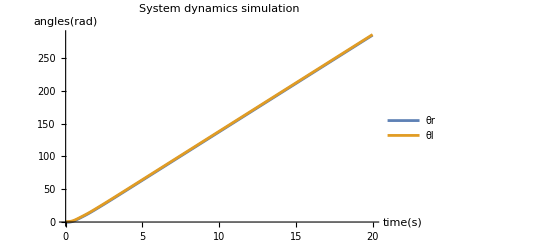

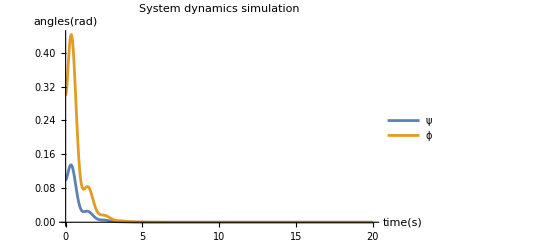

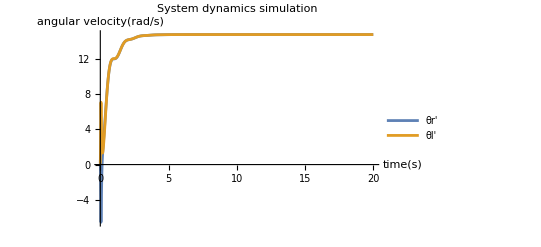

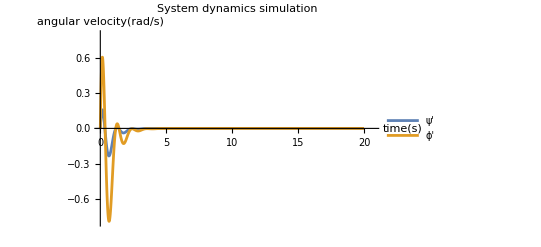

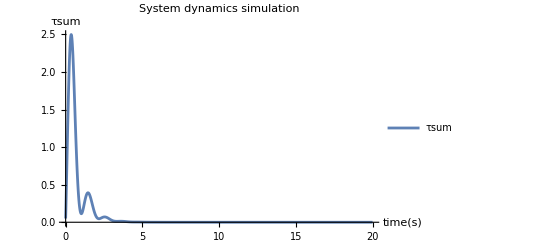

```mathematica
MakeEqual[a_,b_]=(a==b);
CorrespondenceListSysPointEquation=Join[{D[xtrick[t],t]},{ftrick+gtrick.ucontrol}];
SysPointEqns= MakeEqual[#[[1]], #[[2]]]&/@Transpose[CorrespondenceListSysPointEquation];
SysPointEqns[[9]]//MatrixForm
tsim=20;
DynEqs={
 SysPointEqns[[5]],
SysPointEqns[[6]],
 SysPointEqns[[7]],
 SysPointEqns[[8]],
SysPointEqns[[9]]
};
InitialConditions={
(*θr[0]==0.1,
θl[0]==0.1,
ψ[0]==0,
ϕ[0]==0,
θr'[0]==0.5,
θl'[0]==0.1,
ψ'[0]==0,
ϕ'[0]==0,
τsum[0] == 0.4*)

θr[0]==0.1,
θl[0]==0.1,
ψ[0]==0.1,
ϕ[0]==0.3,
θr'[0]==0.5,
θl'[0]==0.1,
ψ'[0]==0,
ϕ'[0]==0,
τsum[0] == 0.05
};

pendulumsolutionnormalform=NDSolveValue[
Join[DynEqs,InitialConditions]/.params,
{θr,θl,ψ,ϕ,θr',θl',ψ',ϕ', τsum},
{t,0,tsim}]


(*ListLinePlot[{pendulumsolutionnormalform[[1]],pendulumsolutionnormalform[[2]]}, PlotLegends->{θr,θl}]
ListLinePlot[{pendulumsolutionnormalform[[3]],pendulumsolutionnormalform[[4]]}, PlotLegends->{ψ,ϕ}]
ListLinePlot[{pendulumsolutionnormalform[[5]],pendulumsolutionnormalform[[6]], pendulumsolutionnormalform[[7]],pendulumsolutionnormalform[[8]], pendulumsolutionnormalform[[9]]}, PlotLegends->{θr',θl',ψ',ϕ'}]*)

tsim=20
sol1=pendulumsolutionnormalform[[1]];
sol2=pendulumsolutionnormalform[[2]];
sol3=pendulumsolutionnormalform[[3]];
sol4=pendulumsolutionnormalform[[4]];
sol5=pendulumsolutionnormalform[[9]];
solution={θr->sol1,θl->sol2,ψ->sol3,ϕ->sol4,θr'->sol1',θl'->sol2',ψ'->sol3',ϕ'->sol4' , τsum -> sol5};
xdnum=xd/.solution/.params;
ydnum=yd/.solution/.params;
xnumerical=NDSolveValue[{xnum'[t]== xdnum,xnum[0]== 0},{xnum},{t,0,tsim}];
ynumerical=NDSolveValue[{ynum'[t]== ydnum,ynum[0]== 0},{ynum},{t,0,tsim}];
solutions=Join[solution,{x-> First[xnumerical], y-> First[ynumerical]}];
SetOptions[ListLinePlot,BaseStyle->FontSize->14];
ListLinePlot[{sol1,sol2}, PlotLegends->{θr,θl},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol3,sol4}, PlotLegends->{ψ,ϕ},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol1',sol2'}, PlotLegends->{θr',θl'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol3',sol4'}, PlotLegends->{ψ',ϕ'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation", PlotRange->{{0,20.7},{-0.8,0.8}}]
ListLinePlot[sol5, PlotLegends->{τsum},AxesLabel->{time [s],"τsum"}, PlotLabel-> "System dynamics simulation"]
```

System simulation

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

20

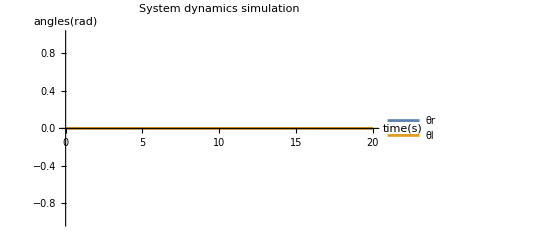

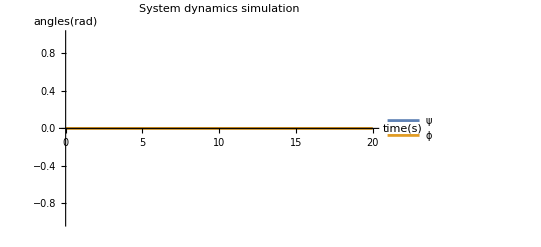

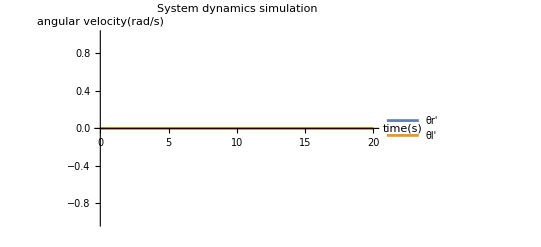

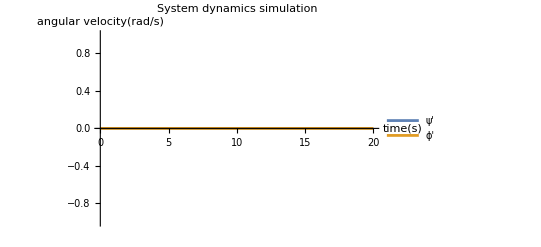

```mathematica
MakeEqual[a_,b_]=(a==b);
LinSysEquation=Join[{D[x[t],t]},{f}];
LinSysEqns= MakeEqual[#[[1]], #[[2]]]&/@Transpose[LinSysEquation];
tsim = 20;
DynEqsLin={
LinSysEqns[[5]],
LinSysEqns[[6]],
LinSysEqns[[7]],
LinSysEqns[[8]]
};

(* Equilibrium point *)
InitialConditionsLin={
θr[0]==0,
θl[0]==0,
ψ[0]==0,
ϕ[0]==0,
θr'[0]==0,
θl'[0]==0,
ψ'[0]==0,
ϕ'[0]==0
};

pendulumsolutionnormalform=NDSolveValue[
Join[DynEqsLin,InitialConditionsLin]/.params,
{θr,θl,ψ,ϕ,θr',θl',ψ',ϕ'},
{t,0,tsim}]

tsim=20
sol1=pendulumsolutionnormalform[[1]];
sol2=pendulumsolutionnormalform[[2]];
sol3=pendulumsolutionnormalform[[3]];
sol4=pendulumsolutionnormalform[[4]];
solution={θr->sol1,θl->sol2,ψ->sol3,ϕ->sol4,θr'->sol1',θl'->sol2',ψ'->sol3',ϕ'->sol4'};
xdnum=xd/.solution/.params;
ydnum=yd/.solution/.params;
xnumerical=NDSolveValue[{xnum'[t]== xdnum,xnum[0]== 0},{xnum},{t,0,tsim}];
ynumerical=NDSolveValue[{ynum'[t]== ydnum,ynum[0]== 0},{ynum},{t,0,tsim}];
solutions=Join[solution,{x-> First[xnumerical], y-> First[ynumerical]}];
SetOptions[ListLinePlot,BaseStyle->FontSize->14];
ListLinePlot[{sol1,sol2}, PlotLegends->{θr,θl},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation" ]
ListLinePlot[{sol3,sol4}, PlotLegends->{ψ,ϕ},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol1',sol2'}, PlotLegends->{θr',θl'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol3',sol4'}, PlotLegends->{ψ',ϕ'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation"]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

20

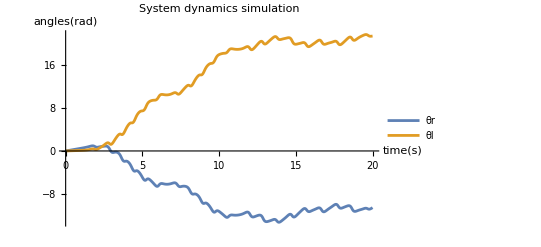

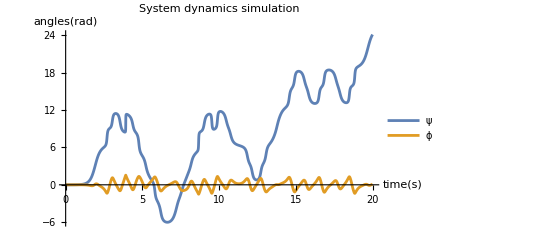

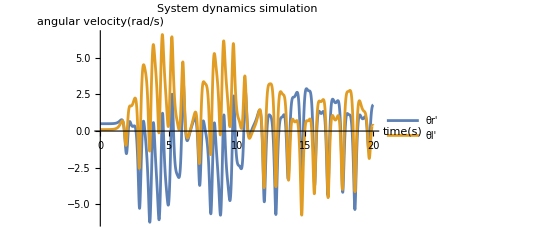

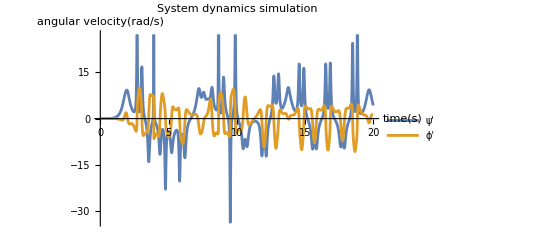

```mathematica
(* Different initial conditions*)
InitialConditionsLin={
θr[0]==0,
θl[0]==0,
ψ[0]==0,
ϕ[0]==0,
θr'[0]==0.5,
θl'[0]==0.1,
ψ'[0]==0,
ϕ'[0]==0
};

pendulumsolutionnormalform=NDSolveValue[
Join[DynEqsLin,InitialConditionsLin]/.params,
{θr,θl,ψ,ϕ,θr',θl',ψ',ϕ'},
{t,0,tsim}]

tsim=20
sol1=pendulumsolutionnormalform[[1]];
sol2=pendulumsolutionnormalform[[2]];
sol3=pendulumsolutionnormalform[[3]];
sol4=pendulumsolutionnormalform[[4]];
solution={θr->sol1,θl->sol2,ψ->sol3,ϕ->sol4,θr'->sol1',θl'->sol2',ψ'->sol3',ϕ'->sol4'};
xdnum=xd/.solution/.params;
ydnum=yd/.solution/.params;
xnumerical=NDSolveValue[{xnum'[t]== xdnum,xnum[0]== 0},{xnum},{t,0,tsim}];
ynumerical=NDSolveValue[{ynum'[t]== ydnum,ynum[0]== 0},{ynum},{t,0,tsim}];
solutions=Join[solution,{x-> First[xnumerical], y-> First[ynumerical]}];
SetOptions[ListLinePlot,BaseStyle->FontSize->14];
ListLinePlot[{sol1,sol2}, PlotLegends->{θr,θl},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol3,sol4}, PlotLegends->{ψ,ϕ},AxesLabel->{time [s],angles[rad]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol1',sol2'}, PlotLegends->{θr',θl'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation"]
ListLinePlot[{sol3',sol4'}, PlotLegends->{ψ',ϕ'},AxesLabel->{time [s],angular velocity[rad/s]}, PlotLabel-> "System dynamics simulation"]
```

### Approximate linearization

```mathematica
MakeEqual[a_,b_]=(a==b);
dinamica=Join[{D[x[t],t]},{f+g.u}];
uscita=Join[{y},{h}];
SysPointEqns1= MakeEqual[#[[1]], #[[2]]]&/@Transpose[dinamica];
(*SysPointEqns2= MakeEqual[#[[1]], #[[2]]]&/@Transpose[uscita];*)
tsim=20;
DynEqs={
 SysPointEqns1[[5]],
SysPointEqns1[[6]],
 SysPointEqns1[[7]],
 SysPointEqns1[[8]]
};
model["DynEqs"];
EquilibriumValues = {θr0->0, θl0-> 0,ψ0-> 0,ϕ0-> 0,θrd0->0, θld0-> 0,ψd0-> 0,ϕd0-> 0};
ss=SystemModelLinearize[model,"EquilibriumValues"];

model = StateSpaceModel[DynEqs,x[t],{u[[1]],u[[2]]},{h[[1]],h[[2]]},t]/.params

obsMatrix = ObservabilityMatrix[model];
MatrixRank[obsMatrix]

ragMatrix = ControllabilityMatrix[model];
MatrixRank[ragMatrix]
```

0000100000000001000000000010000000000100000-14.0143000013.3373-0.638914000-14.01430000-0.63891413.33730021.0214000000000030.03060000-4.08163-4.0816300100000000001000000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2281FalseFalseFalseAutomaticNone,{{θr[t],0},{θl[t],0},{ψ[t],0},{ϕ[t],0},x_1,x_2,x_3,x_4},{{τl[t],0},{τr[t],0}},Automatic,t

4

6